```mathematica
Nt = 512; 
ti = 0; tf = 5; 
deltat = (tf - ti) /Nt ;
Nx = 128;
xi = -40; xf = 40; 
deltax = (xf - xi) / Nx; 
c =  1;

(*For Max Eigenvalue Plots*)
rs = Table[0.1*i,{i,1,200}];(*200 for Limits*)

maxevalsLD2 = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsPI = Table[0,{i,1,Length[rs]}];
maxevalsNew = Table[0,{i,1,Length[rs]}];



Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

selectwidth = 3;
diffOrder = 4;
deriv = 2;


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);
(LP2=NDSolve`FiniteDifferenceDerivative[Derivative[4],grid,"DifferenceOrder"->diffOrder - 2]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);
LPX2 = LP2*((-1)^4)*(r*(Δx)^4);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

gn2 = (LPX2[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX2 = Table[RotateRight[gn2,i],{i,-selectwidth,selectwidth}];
LPX2[[1,-1]]=0;
LPX2[[1,-2]]=0;
LPX2[[2,-1]]=0;
LPX2[[-1,1]]=0;
LPX2[[-1,2]]=0;
LPX2[[-2,1]]=0;
LPX2[[-3,1]] = 0;
LPX2[[-2,2]] = 0;
LPX2[[-1,3]] = 0;
LPX2[[1,-3]] = 0;
LPX2[[2,-2]] = 0;
LPX2[[3,-1]] = 0;


IP=IdentityMatrix[Length[LPX]];

(Mn=Inverse[IP-(ⅈ * LPX)/4  - LPX2/48 ].(IP+(ⅈ * LPX)/4- LPX2/48));

fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,1,Nx},{j,1,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - (n - 1)]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + (n - 1)]]  ,{n,1,selectwidth}],{i,1,Nx},{j,1,Nx}];*)
```

```mathematica
(*New Haris Method*)
r=.;
totalpoints=7;
selectwidth = 3;
middlepoint=0;
x0=0;
grid=x0+(Range[totalpoints]-middlepoint)Δx;
D2=Δx^2 NDSolve`FiniteDifferenceDerivative[Derivative[2],grid,"DifferenceOrder"->5]@"DifferentiationMatrix"//Normal;
Id=IdentityMatrix[totalpoints];
```

```mathematica
Linf=MatrixExp[r*D2]//Simplify;
fmid=Linf[[(totalpoints+1) / 2]]
fmid[[1]]
```

{1/180 r (2-15 r+30 r^2),-(3 r)/20+r^2-r^3,1/4 r (6-13 r+10 r^2),1/18 (18-49 r+84 r^2-60 r^3),1/4 r (6-13 r+10 r^2),-(3 r)/20+r^2-r^3,1/180 r (2-15 r+30 r^2)}

1/180 r (2-15 r+30 r^2)

```mathematica
middlepoint = 4;
MP2 = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fmid[[k]] + (Subscript[δ, i,(j-k)])fmid[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fmid[[middlepoint]],{i,1,Nx},{j,1,Nx}];
```

```mathematica
Do[
deltat = (deltax^2) * rs[[p]];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- x^2+ⅈ x);


(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp,"DifferenceOrder"->1, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);


(* LD2 *)
ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];

evals = Eigenvalues[N[MLD2]];

maxevalsLD2[[p]] = Max[Abs[evals]];

(*PI*)
MPtest = N[MP//.{N[r -> rs[[p]],32]},32];

evalsPI = Eigenvalues[N[MPtest]];

maxevalsPI[[p]] = Max[Abs[evalsPI]];

(*New*)
MPtest2 =  N[MP2//.{N[r -> ⅈ *rs[[p]],32]},32];

evalsNew = Eigenvalues[N[MPtest2]];

maxevalsNew[[p]] = Max[Abs[evalsNew]];


Print["Finished "<>ToString[rs[[p]]]];


,{p,1,Length[rs]}]


(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsLD2,maxevalsLD2,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];*)
(*Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

Finished 0.1

Finished 0.2

Finished 0.3

Finished 0.4

Finished 0.5

Finished 0.6

Finished 0.7

Finished 0.8

Finished 0.9

Finished 1.

Finished 1.1

Finished 1.2

Finished 1.3

Finished 1.4

Finished 1.5

Finished 1.6

Finished 1.7

Finished 1.8

Finished 1.9

Finished 2.

Finished 2.1

Finished 2.2

Finished 2.3

Finished 2.4

Finished 2.5

Finished 2.6

Finished 2.7

Finished 2.8

Finished 2.9

Finished 3.

Finished 3.1

Finished 3.2

Finished 3.3

Finished 3.4

Finished 3.5

Finished 3.6

Finished 3.7

Finished 3.8

Finished 3.9

Finished 4.

Finished 4.1

Finished 4.2

Finished 4.3

Finished 4.4

Finished 4.5

Finished 4.6

Finished 4.7

Finished 4.8

Finished 4.9

Finished 5.

Finished 5.1

Finished 5.2

Finished 5.3

Finished 5.4

Finished 5.5

Finished 5.6

Finished 5.7

Finished 5.8

Finished 5.9

Finished 6.

Finished 6.1

Finished 6.2

Finished 6.3

Finished 6.4

Finished 6.5

Finished 6.6

Finished 6.7

Finished 6.8

Finished 6.9

Finished 7.

Finished 7.1

Finished 7.2

Finished 7.3

Finished 7.4

Finished 7.5

Finished 7.6

Finished 7.7

Finished 7.8

Finished 7.9

Finished 8.

Finished 8.1

Finished 8.2

Finished 8.3

Finished 8.4

Finished 8.5

Finished 8.6

Finished 8.7

Finished 8.8

Finished 8.9

Finished 9.

Finished 9.1

Finished 9.2

Finished 9.3

Finished 9.4

Finished 9.5

Finished 9.6

Finished 9.7

Finished 9.8

Finished 9.9

Finished 10.

Finished 10.1

Finished 10.2

Finished 10.3

Finished 10.4

Finished 10.5

Finished 10.6

Finished 10.7

Finished 10.8

Finished 10.9

Finished 11.

Finished 11.1

Finished 11.2

Finished 11.3

Finished 11.4

Finished 11.5

Finished 11.6

Finished 11.7

Finished 11.8

Finished 11.9

Finished 12.

Finished 12.1

Finished 12.2

Finished 12.3

Finished 12.4

Finished 12.5

Finished 12.6

Finished 12.7

Finished 12.8

Finished 12.9

Finished 13.

Finished 13.1

Finished 13.2

Finished 13.3

Finished 13.4

Finished 13.5

Finished 13.6

Finished 13.7

Finished 13.8

Finished 13.9

Finished 14.

Finished 14.1

Finished 14.2

Finished 14.3

Finished 14.4

Finished 14.5

Finished 14.6

Finished 14.7

Finished 14.8

Finished 14.9

Finished 15.

Finished 15.1

Finished 15.2

Finished 15.3

Finished 15.4

Finished 15.5

Finished 15.6

Finished 15.7

Finished 15.8

Finished 15.9

Finished 16.

Finished 16.1

Finished 16.2

Finished 16.3

Finished 16.4

Finished 16.5

Finished 16.6

Finished 16.7

Finished 16.8

Finished 16.9

Finished 17.

Finished 17.1

Finished 17.2

Finished 17.3

Finished 17.4

Finished 17.5

Finished 17.6

Finished 17.7

Finished 17.8

Finished 17.9

Finished 18.

Finished 18.1

Finished 18.2

Finished 18.3

Finished 18.4

Finished 18.5

Finished 18.6

Finished 18.7

Finished 18.8

Finished 18.9

Finished 19.

Finished 19.1

Finished 19.2

Finished 19.3

Finished 19.4

Finished 19.5

Finished 19.6

Finished 19.7

Finished 19.8

Finished 19.9

Finished 20.

```mathematica
maxevalsLD2 = Join[{1},maxevalsLD2];
rsLD2 = Join[{0},rs];

maxevalsPI = Join[{1},maxevalsPI];
rsPI = Join[{0},rs];

maxevalsNew = Join[{1},maxevalsNew];
rsNew = Join[{0},rs];
```

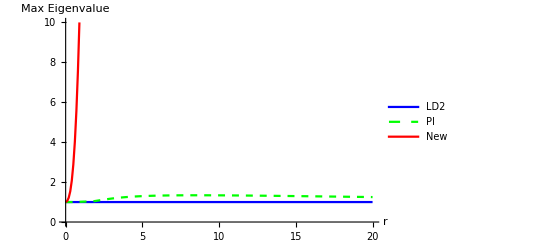

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}], Transpose[{rsNew,maxevalsNew}]},PlotStyle->{Blue, {Green, Dashed}, Red}, PlotLegends->{"LD2", "PI", "New"}, AxesLabel->{"r", "Max Eigenvalue"}, PlotRange->{All,{0,10}}]
```

```mathematica
differencesPI = Table[0,{i,2,Length[maxevalsPI]}];
differencesNew = Table[0,{i,2,Length[maxevalsNew]}];
Do[
differencesPI[[i - 1]] = maxevalsPI[[i]] - maxevalsPI[[i-1]];
differencesNew[[i - 1]] = maxevalsNew[[i]] - maxevalsNew[[i-1]];
,{i,2,Length[maxevalsPI]}]
```

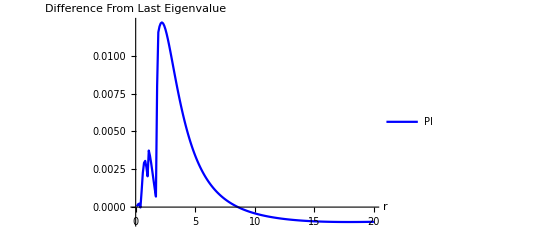

```mathematica
ListLinePlot[{Transpose[{rs,differencesPI}]},PlotStyle->{Blue, {Green, Dashed}, Red}, PlotLegends->{"PI", "New"}, AxesLabel->{"r", "Difference From Last Eigenvalue"}]
```

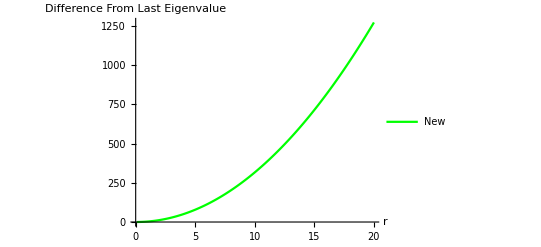

```mathematica
ListLinePlot[{Transpose[{rs,differencesNew}]},PlotStyle->{Green}, PlotLegends->{"New"}, AxesLabel->{"r", "Difference From Last Eigenvalue"}]
```

```mathematica
rs
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.}

```mathematica
rs[[19]]
```

1.9

```mathematica
differencesPI[[19]]
```

0.0115499

```mathematica
differencesPI
```

{0.0000443694,0.000184387,0.000230665,-0.0000243394,0.00106787,0.00226452,0.00292126,0.00305286,0.00263402,0.00203348,0.00373557,0.00338581,0.00290184,0.00234729,0.00177057,0.00120968,0.000694416,0.00799071,0.0115499,0.0119307,0.0121377,0.0121977,0.0121362,0.0119765,0.0117387,0.0114407,0.0110973,0.0107211,0.0103226,0.00991037,0.0094912,0.0090707,0.00865322,0.00824218,0.00784019,0.00744918,0.00707055,0.00670527,0.00635395,0.00601691,0.00569426,0.00538592,0.00509168,0.00481122,0.00454417,0.00429008,0.00404847,0.00381882,0.00360064,0.00339338,0.00319655,0.00300961,0.00283209,0.00266348,0.00250333,0.00235119,0.00220662,0.00206922,0.00193859,0.00181436,0.00169619,0.00158374,0.00147668,0.00137474,0.00127761,0.00118505,0.0010968,0.00101262,0.00093229,0.000855609,0.000782375,0.000712406,0.000645527,0.000581575,0.000520396,0.000461846,0.000405789,0.000352097,0.000300649,0.000251332,0.00020404,0.000158672,0.000115132,0.0000733329,0.0000331894,-5.37731×10^-6,-0.0000424421,-0.0000780753,-0.000112344,-0.00014531,-0.000177033,-0.000207569,-0.000236971,-0.000265289,-0.00029257,-0.00031886,-0.000344199,-0.000368629,-0.000392188,-0.000414911,-0.000436832,-0.000457984,-0.000478398,-0.000498102,-0.000517125,-0.000535492,-0.000553228,-0.000570358,-0.000586903,-0.000602886,-0.000618326,-0.000633243,-0.000647656,-0.000661583,-0.000675039,-0.000688042,-0.000700606,-0.000712747,-0.000724478,-0.000735812,-0.000746763,-0.000757343,-0.000767563,-0.000777434,-0.000786968,-0.000796175,-0.000805064,-0.000813645,-0.000821928,-0.00082992,-0.00083763,-0.000845066,-0.000852237,-0.000859149,-0.00086581,-0.000872226,-0.000878404,-0.000884351,-0.000890073,-0.000895575,-0.000900864,-0.000905945,-0.000910824,-0.000915505,-0.000919993,-0.000924294,-0.000928412,-0.000932352,-0.000936118,-0.000939714,-0.000943144,-0.000946413,-0.000949524,-0.000952481,-0.000955288,-0.000957948,-0.000960465,-0.000962842,-0.000965082,-0.000967188,-0.000969164,-0.000971013,-0.000972737,-0.000974339,-0.000975822,-0.000977189,-0.000978442,-0.000979584,-0.000980618,-0.000981545,-0.000982369,-0.000983091,-0.000983713,-0.000984239,-0.00098467,-0.000985008,-0.000985256,-0.000985415,-0.000985487,-0.000985474,-0.000985379,-0.000985202,-0.000984946,-0.000984613,-0.000984204,-0.000983721,-0.000983166,-0.00098254,-0.000981845,-0.000981082,-0.000980253,-0.00097936,-0.000978403,-0.000977385,-0.000976306,-0.000975169,-0.000973974,-0.000972724,-0.000971418,-0.000970058}

```mathematica
maxevalsPI
```

{1,1.00004,1.00023,1.00046,1.00044,1.0015,1.00377,1.00669,1.00974,1.01238,1.01441,1.01814,1.02153,1.02443,1.02678,1.02855,1.02976,1.03045,1.03844,1.04999,1.06193,1.07406,1.08626,1.0984,1.11037,1.12211,1.13355,1.14465,1.15537,1.16569,1.1756,1.1851,1.19417,1.20282,1.21106,1.2189,1.22635,1.23342,1.24013,1.24648,1.2525,1.25819,1.26358,1.26867,1.27348,1.27803,1.28232,1.28636,1.29018,1.29378,1.29718,1.30037,1.30338,1.30621,1.30888,1.31138,1.31373,1.31594,1.31801,1.31995,1.32176,1.32346,1.32504,1.32652,1.32789,1.32917,1.33036,1.33145,1.33246,1.3334,1.33425,1.33504,1.33575,1.33639,1.33697,1.3375,1.33796,1.33836,1.33871,1.33902,1.33927,1.33947,1.33963,1.33974,1.33982,1.33985,1.33985,1.3398,1.33973,1.33961,1.33947,1.33929,1.33908,1.33885,1.33858,1.33829,1.33797,1.33763,1.33726,1.33686,1.33645,1.33601,1.33555,1.33508,1.33458,1.33406,1.33353,1.33297,1.3324,1.33181,1.33121,1.33059,1.32996,1.32931,1.32865,1.32798,1.32729,1.32659,1.32587,1.32515,1.32441,1.32367,1.32291,1.32214,1.32137,1.32058,1.31978,1.31898,1.31816,1.31734,1.31651,1.31567,1.31483,1.31398,1.31312,1.31225,1.31138,1.3105,1.30962,1.30873,1.30783,1.30693,1.30602,1.30511,1.3042,1.30328,1.30235,1.30143,1.30049,1.29956,1.29862,1.29767,1.29673,1.29578,1.29483,1.29387,1.29291,1.29195,1.29099,1.29002,1.28906,1.28809,1.28712,1.28614,1.28517,1.28419,1.28322,1.28224,1.28126,1.28028,1.2793,1.27831,1.27733,1.27635,1.27536,1.27438,1.27339,1.27241,1.27142,1.27044,1.26945,1.26847,1.26748,1.2665,1.26551,1.26453,1.26354,1.26256,1.26158,1.2606,1.25961,1.25863,1.25766,1.25668,1.2557,1.25472,1.25375,1.25277,1.2518,1.25083,1.24986}